```mathematica
Vcc=9;
Vref=0.25Vcc;
Rl = 22*^3;
dRmin=100; (*light*)
dRmax=40*^3; (*dark*)
Rg=20*^3;
R=10.0*^2;
(* For logging ; used Rs=6.7K*)
Vm = ((Vcc/(Rl+dR) + Vref/R)/(1/Rs + 1/R + 1/(Rl+dR)));
(*Vout=Vref (1+Rg/R) - Vcc Rg (Rs/(Rl+dR+Rs))*)
Vout = Vref + Rg/R(Vref-Vm);
mxsol = ToRules[Reduce[(Vout/.{dR->dRmax} )== 6.0, Rs]]
(*Reduce[(Vout/.{dR->dRmin} )== Vref, Rs]*)
Vout/.{mxsol}/.{dR->dRmin}
```

{Rs→6888.89}

{2.60589}

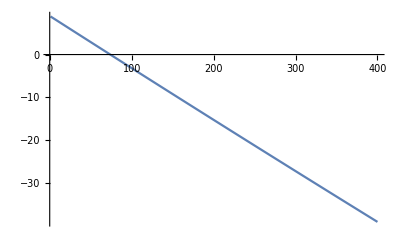

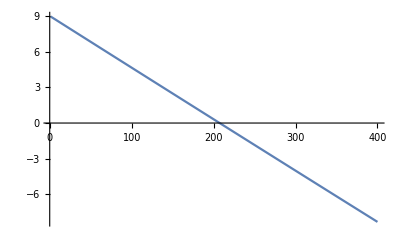

```mathematica
Plot[Vout/.{dR->dRmin}, {Rs, 1, 4*^2}]
Plot[Vout/.{dR->dRmax}, {Rs, 1, 4*^2}]
```

```mathematica
Plot3D[Vout, {dR, dRmin, dRmax}, {Rs, 1, 4*^2}, AxesLabel->Automatic, MeshFunctions->{#3&}, Mesh->{{0.0}}, MeshStyle->Directive[Thick,Red]]
```

-Graphics3D-